```mathematica
Tau = 2 Pi;
Second[lst_]:=lst[[2]];
Middle[xs_]:=xs[[Floor[(Length[xs]+1)/2]]];
WithXRegion[a_,b_][xs_]:=Block[{n=Length[xs]},Table[{a + (b-a) i/n, xs[[i]]},{i,1,n}]];

Exact[a_]:=-Zeta[3]/(4 Tau a^3)//N;
ParallelPlates[a_,L_,w_]:=Module[{n,r,  e,da,v,d,  P,idx,rhs,eqs,vars,sol},
If[w==0,Return[0]];
n=Max[30,10L/a // Ceiling];
r=L/n;
idx=Floor[n/2];
d[i_,j_]:=r(i-j);

e[i_,j_]:=-w/Tau BesselK[1,w Sqrt[a^2+d[i,j]^2]] / Sqrt[1 + (d[i,j]/a)^2]//N;
da[i_,j_]:=If[i==j,0 2/Tau (EulerGamma - 1 + Log[1/(n w L)]), -2/Tau BesselK[0, w r Abs[i-j]]];
v[i_,j_]:=-1/Tau BesselK[0, w Sqrt[a^2 + d[i,j]^2]]-Sum[r e[k,i]da[k,j], {k,1,n}]//N;

rhs[0,i_]:=-r Sum[e[k,i] P[1,k],{k,1,n}];
rhs[1,i_]:=-r Sum[e[k,i] P[0,k],{k,1,n}]+v[i,idx];
eqs = Table[1/2 P[b,i]==rhs[b,i], {b,0,1},{i,1,n}]//Flatten;
vars=Table[P[b,i],{b,0,1},{i,1,n}]//Flatten;
sol= NSolve[eqs,vars]//First;
w^2 /Tau (Table[P[0,i]/.sol,{i,1,n}])
];

Pressure[a_,L_,w_]:=ParallelPlates[a,L,w]//Middle;

Force[a_,L_]:=Module[{integrand, ubound, dx, n, x},
integrand[w_]:=Pressure[a,L,w];
n = 20;
ubound=6;
dx = ubound/n//N;
x=Table[integrand[ubound * j/n],{j,1,n}];
dx/3 * (2 Sum[x[[2 j]],{j,1,n/2-1}]+4 Sum[x[[2j-1]],{j,1,n/2}]+x[[n]])
];
```

```mathematica
Force[1,10]
```

0.0167414

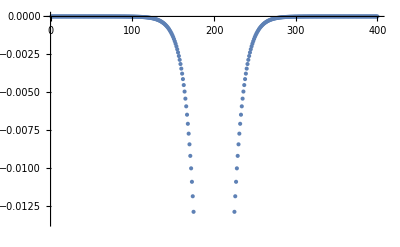

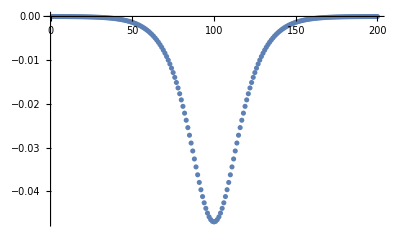

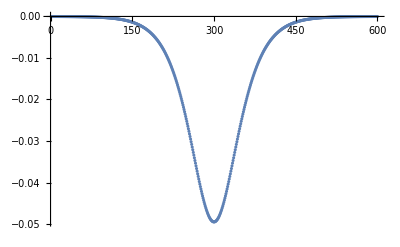

```mathematica
ParallelPlates[0.5,20,2]//ListPlot[#]&
```

```mathematica
TestPowerDependency[Force[#,10]&,0.5,3,5]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

ListPlot::lpn: $Aborted is not a list of numbers or pairs of numbers.

Plot::plln: Limiting value $Aborted in {x,xmin$40903,xmax$40903} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[$Aborted],Plot[fit$40360[x],{x,xmin$40903,xmax$40903}]}].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Plot::plln: Limiting value $Aborted in {x,xmin$40903,xmax$40903} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[$Aborted],Plot[fit$40360[x],{x,xmin$40903,xmax$40903}]}].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

{Show[{ListPlot[$Aborted],Plot[fit$40360[x],{x,xmin$40903,xmax$40903}]}],-LinearModelFit[$Aborted,x,x][0]+LinearModelFit[$Aborted,x,x][1],R^2 = LinearModelFit[$Aborted, x, x][RSquared]}

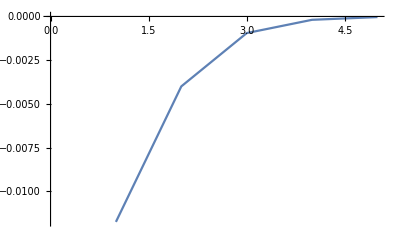

```mathematica
Table[Pressure[1,20,w],{w,1,5}]//ListLinePlot
```

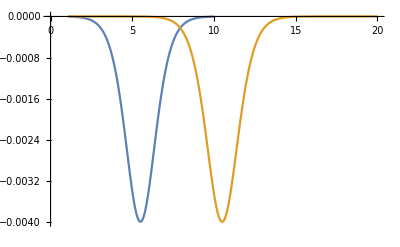

```mathematica
{ParallelPlates[1, 10, 2]//ScaleToRegion[1,10],ParallelPlates[1,20,2]//ScaleToRegion[1,20]}//ListLinePlot
```

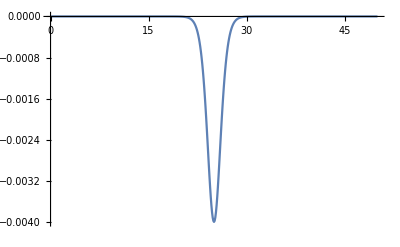

```mathematica
Block[{pts=ParallelPlates[1,50,2]//WithXRegion[0,50]},
Show[ListLinePlot[pts,PlotRange->All],ListLinePlot[Table[Middle[pts],{i,1,Length[pts]}]]]
]
```